Finite element models of elasto-plastic materials
Created by Michele Marino, Department of Civil Engineering and Computer Science, University of Rome Tor Vergata, Italy
Date: 13 December 2021 - Contact: m.marino@ing.uniroma2.it

# Elements

## Q1EPS - Elasto-plasticity (small strain)

### Initialization

```mathematica
<<AceGen`;

SMSInitialize["Q1EPS","Environment"-> "AceFEM","Mode"-> "Optimal"];

SMSTemplate["SMSTopology"->"Q1",
(*Initialize domain data for material parameters*)
"SMSDomainDataNames"-> {"E -Young","ν -Poisson", "σYO -yield", "H -Hardening"},
 "SMSDefaultData" -> {100,0.49,1,10},

(*Time history element data*)
"SMSNoTimeStorage"-> lhg es$$["id","NoIntPoints"],
"SMSPostIterationCall"->True,

(*Expected symmetry in tangent stiffness*)
"SMSSymmetricTangent"->True
];

RelevantNumbers[]:=(
nen=SMSNoNodes; 
ndim=SMSNoDimensions; 
ndof=SMSNoDOFGlobal;
nip=SMSIO["No. integration points"];
(*Number of element hystory variables*)
nhg =7; 
lhg=nhg+1;
)
```

### Element definitions

```mathematica
ElementDefinitions[Ig_]:=(
(*MATERIAL AND ELEMENT DATA*)
{Ee,ν,σYO,H}⊨SMSIO["Domain data"];

{ξ,η,ζ}⊨SMSIO["Integration point"[Ig]];
wgp⊨SMSIO["Integration weight"[Ig]];

{𝕏IO,𝕦IO}⊨SMSIO["All coordinates and DOFs"];
𝕦e=Flatten[𝕦IO];

(*SHAPE FUNCTIONS*)
Ξn⊨{{-1,-1},{1,-1},{1,1},{-1,1}};
ℕh⊨Table[1/4(1+ξ Ξn⟦i,1⟧)(1+η Ξn⟦i,2⟧),{i,1,nen}];

(*ISOPARAMETRIC MAPPING*)
𝕏⊢SMSFreeze[ℕh.𝕏IO];
𝕁e⊨SMSD[𝕏,{ξ,η}]; 
Jed⊨SMSDet[𝕁e];

(*KINEMATICS AND CONSTITUTIVE BEHAVIOUR*)
𝕦⊨ℕh.𝕦IO;
ℍ⊨SMSD[𝕦,𝕏,"Dependency"->{{ξ,η},𝕏,SMSInverse[𝕁e]}];
SMSFreeze[𝔻,(ℍ+Transpose[ℍ])/2,"Symmetric"-> True];

ϵ=SMSVariables[𝔻];
GaussPointComputation[Ig];
Ψe⊨ElastoPlastic["EN",𝕙g];
)

ElastoPlastic[task_,𝕙g_]:=(
(*History variables*)
𝔻p={{𝕙g⟦1⟧,𝕙g⟦3⟧},{𝕙g⟦3⟧,𝕙g⟦2⟧}};
(*α⊢SMSFreeze[𝕙g⟦4⟧];*)
α⊢SMSFreeze[{{𝕙g⟦4⟧,𝕙g⟦6⟧},{𝕙g⟦6⟧,𝕙g⟦5⟧}},"Symmetric"->True];
(*λ=𝕙g⟦5⟧;*)
λ=𝕙g⟦7⟧;

(*Pseudo-energy*)
SMSFreeze[𝔻e,𝔻-𝔻p,"Symmetric"->True];
{λe,μe}⊢SMSHookeToLame[Ee,ν];
(*Ψe⊨λe/2 (Tr[𝔻e])^2+μe Tr[𝔻e.𝔻e]+1/2 H α^2;*)
(*Ψe⊨λe/2 (Tr[𝔻e])^2+μe Tr[𝔻e.𝔻e]+1/2 Transpose[α]H α;*)
Ψe⊨λe/2 (Tr[𝔻e])^2+μe Tr[𝔻e.𝔻e]+1/2 H α.α;
If[task=="EN", Return[Ψe]];

(*Static quantities*)
SMSFreeze[σ,SMSD[Ψe,𝔻e,
		"Symmetric"->True],
			"Symmetric"->True];
SMSFreeze[q,-SMSD[Ψe,α,"Symmetric"->True]];

(*Yield function*)
σdev=σ-1/3 IdentityMatrix[ndim] Tr[σ];
(*fg⊨SMSSqrt[3/2 Tr[σdev.σdev]]-(σYO-q);*)
fg⊨SMSSqrt[3/2 Norm[σdev-q]]-(σYO);(* LA RADICE ?????*)
(*fg⊨SMSSqrt[3/2 Tr[Transpose[σdev-q].(σdev-q)]]-(σYO);*)
If[task=="f", Return[fg]];

(*Flow rule*)
𝕟σ=SMSD[fg,σ,"Symmetric"->True];
𝕟q=SMSD[fg,q];
𝔻pn={{𝕙gnIO⟦1⟧,𝕙gnIO⟦3⟧},
{𝕙gnIO⟦3⟧,𝕙gnIO⟦2⟧}};
(*αn=𝕙gnIO⟦4⟧;*)
αn={{𝕙gnIO⟦4⟧,𝕙gnIO⟦6⟧},
{𝕙gnIO⟦6⟧,𝕙gnIO⟦5⟧}};
λn=𝕙gnIO⟦7⟧;
ℚϵ=𝔻p-𝔻pn-(λ-λn)𝕟σ;
Qq=α-αn-(λ-λn)𝕟q;
Qλ=fg;
ℚ={ℚϵ⟦1,1⟧,ℚϵ⟦2,2⟧,ℚϵ⟦1,2⟧,Qq⟦1,1⟧,Qq⟦2,2⟧,Qq⟦1,2⟧,Qλ};
If[task=="Q", Return[ℚ]];
)

GaussPointComputation[Ig_]:=(
Ihg⊢SMSInteger[(Ig-1)lhg];
(*Algorithm parameters*)
tol⊢SMSReal[rdata$$["SubIterationTolerance"]];
iNR⊢SMSInteger[idata$$["Iteration"]];
(*Previous time step*)
𝕙gnIO⊢SMSIO["Element time dependent data n"[Table[Ihg+i,{i,nhg}]]];
staten⊢SMSIO["Element time dependent data n"[Ihg+nhg+1]];
(*Initialize trial: plastic variables are freezed*)
ftr⊨ElastoPlastic["f",𝕙gnIO];

SMSIf[(iNR==1 && staten==0)||(iNR>1 && ftr<tol)];
	(*Elastic step*)
	𝕙g⫤𝕙gnIO;
	SMSIO[Join[𝕙g,{0}],"Export to",
			"Element time dependent data"[Table[Ihg+i,{i,lhg}]]];
SMSElse[];
	(*Plastic step*)
	𝕙gb⫤𝕙gnIO;
	SMSDo[jNR,1,30,1,𝕙gb];
		ℚg⊨ElastoPlastic["Q",𝕙gb];
		𝔸g⊨SMSD[ℚg,𝕙gb];
		Δ𝕙⊨SMSLinearSolve[𝔸g,-ℚg];
		𝕙gb⊣𝕙gb+Δ𝕙;
		
		SMSIf[SMSSqrt[Δ𝕙.Δ𝕙]<tol];
			SMSIO[Join[𝕙gb,{1}], "Export to", 
				  "Element time dependent data"[Table[Ihg+i,{i,lhg}]]];
			D𝕙Dϵ⫤SMSLinearSolve[𝔸g,-SMSD[ℚg,ϵ,"Constant"->𝕙gb]];
			SMSBreak[];
		SMSEndIf[D𝕙Dϵ];
		
		SMSIf[jNR=="29"];
		SMSExport[{1,2},{idata$$["SubDivergence"],idata$$["ErrorStatus"]}];
			SMSBreak[];
		SMSEndIf[];
	SMSEndDo[𝕙gb,D𝕙Dϵ];

	𝕙g⊣SMSFreeze[𝕙gb,"Dependency"->{ϵ,D𝕙Dϵ}];
SMSEndIf[𝕙g];
)
```

### Tangent and Residual

```mathematica
SMSStandardModule["Tangent and residual"];
RelevantNumbers[];
SMSDo[Ig,1,nip];

ElementDefinitions[Ig];
SMSDo[
Rgi⊨Jed wgp SMSD[Ψe,𝕦e,i,"Constant"->𝕙g];
SMSIO[Rgi,"Add to","Residual"[i]];
SMSDo[
Kgij⊨ SMSD[Rgi,𝕦e,j];
SMSIO[Kgij,"Add to","Tangent"[i,j]];
,{j,i,ndof}];
,{i,1,ndof}];
SMSEndDo[];
```

### Post-processing

```mathematica
SMSStandardModule["Postprocessing"];
RelevantNumbers[];
SMSDo[Ig,1,nip];

ElementDefinitions[Ig];
𝔻p⊨𝔻-𝔻e;
σ⊨SMSD[Ψe,𝔻e,"Symmetric"->True];
σdev⊨σ-1/3 IdentityMatrix[ndim]Tr[σ];
σVM⊨SMSSqrt[3/2 Tr[σdev.σdev]];

SMSIO[
{"ϵxx"->𝔻⟦1,1⟧,"ϵxy"->𝔻⟦1,2⟧,"ϵyy"->𝔻⟦2,2⟧,"ϵexx"->𝔻e⟦1,1⟧,"ϵexy"->𝔻e⟦1,2⟧,"ϵeyy"->𝔻e⟦2,2⟧,"ϵpxx"->𝔻p⟦1,1⟧,"ϵpxy"->𝔻p⟦1,2⟧,"ϵpyy"->𝔻p⟦2,2⟧,"σxx"->σ⟦1,1⟧,"σxy"->σ⟦1,2⟧,"σyy"->σ⟦2,2⟧,"σVM"-> σVM,"α"->α,"λ"->λ,"Ψe"->Ψe}
,"Export to","Integration point post"[Ig]];

SMSEndDo[];

𝕦h⊨Transpose[𝕦IO];
SMSIO[{"DeformedMeshX"->𝕦h⟦1⟧,"DeformedMeshY"->𝕦h⟦2⟧,"u"->𝕦h⟦1⟧,"v"->𝕦h⟦2⟧},"Export to","Nodal point post"];
```

Part::partd: Part specification σ⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification σ⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification σ⟦2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification 𝕦h⟦1⟧ is longer than depth of object.

Part::partd: Part specification 𝕦h⟦2⟧ is longer than depth of object.

Part::partd: Part specification 𝕦h⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

### Code generation

```mathematica
SMSWrite[];
```

File: Q1EPS.c  Size: 20953  Time: 10
Method | SKR | SPP
No.Formulae | 246 | 185
No.Leafs | 3340 | 2548

# FEM Simulations

## Patch test

### Definition of Mesh, Loads and Boundary Conditions

```mathematica
L=1;
ϵmax=0.1;

<<AceFEM`;
SMTInputData[];
SMTAddDomain["Ωc","Q1EPS",{"E *"-> 100,"ν *"-> 0.3,"σYO *"->5,"H *"->10}];

SMTAddNode[L{{0.0,0.0},{0.0,1.0},{0.2,0.15},{0.75,0.3},{1.0,0.0},{0.25,0.7},{0.75,0.75},{1.0,1.0}}];
SMTAddElement[{{"Ωc",{1,5,4,3}},{"Ωc",{1,3,6,2}},{"Ωc",{2,6,7,8}},{"Ωc",{8,7,4,5}},{"Ωc",{7,6,3,4}}}];

SMTAddEssentialBoundary[Point[{0,0},"D"],1->0,2->0];
SMTAddEssentialBoundary[Point[{0,L},"D"],1->0,2->ϵmax L];
SMTAddEssentialBoundary[Point[{L,0},"D"],2->0];
SMTAddEssentialBoundary[Point[{L,L},"D"],2->ϵmax L];
SMTAnalysis[];
```

### Solution algorithm (loading-unloading, adaptive)

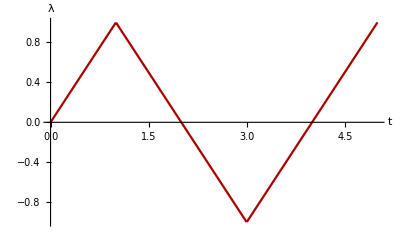

```mathematica
tMax=5;
λf[t_]:=If[OddQ[Floor[(t+1)/2]],1,-1] (2 Floor[(t+1)/2]-t);
Plot[λf[t],{t,0,tMax},AxesLabel->{"t","λ"},
PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black]]
```

```mathematica
Clear[σ]; σ={{0,0}};
t0=0.1;ΔtMin=0.0001;ΔtMax=0.1;
tolNR=10^-8;maxNR=50;targetNR=15;
SMTNextStep["t"->t0,"λ[t]"->λf];
While[ 
While[
step=SMTConvergence[tolNR,maxNR,{"Adaptive Time",targetNR,ΔtMin,ΔtMax,tMax}]
,SMTNewtonIteration[];];
If[step⟦4⟧==="MinBound",SMTStatusReport["Analyze"];SMTStepBack[];]; 
step⟦3⟧ ,If[step⟦1⟧
,SMTStepBack[];,
AppendTo[σ,{SMTPostData["ϵyy",{L/2,L/2}],SMTPostData["σyy",{L/2,L/2}]}];
];
SMTNextStep["Δt"->step⟦2⟧,"λ[t]"->λf];];
AppendTo[σ,{SMTPostData["ϵyy",{L/2,L/2}],SMTPostData["σyy",{L/2,L/2}]}];
```

### Results

```mathematica
ListLinePlot[σ,AxesLabel->{"ϵyy","σyy"},PlotMarkers->"●",PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black]]
```

-Graphics-

```mathematica
Show[SMTShowMesh["Field"->"ϵyy","DeformedMesh"->True,ImageSize->300],SMTShowMesh["DeformedMesh"->False,"Opacity"->0.3,ImageSize->300]]
```

-Graphics-

## Plate with crack

### Definition of Mesh, Loads and Boundary Conditions

```mathematica
L=10; H=L; 
a=L/4;
points1={{0,0},{L,0},{L,H/2},{0,H/2}};
points2={{0,H/2},{L,H/2},{L,H},{0,H}};
densmesh=100;
```

```mathematica
<<AceFEM`;
SMTInputData[];
SMTAddDomain[
{"Ωc1","Q1EPS",{"E *"-> 100,"ν *"-> 0.3,"σYO *"->5,"H *"->10}}
,
{"Ωc2","Q1EPS",{"E *"-> 100,"ν *"-> 0.3,"σYO *"->5,"H *"->10}}
];
SMTAddMesh[Polygon[points1],"Ωc1","Q1",{densmesh,densmesh/2}];
SMTAddMesh[Polygon[points2],"Ωc2","Q1",{densmesh,densmesh/2}];

q=5;
SMTAddEssentialBoundary[{Line[{{0,0},{L,0}},"D"],2-> 0}];
SMTAddEssentialBoundary[{Line[{{0,0},{0,H}},"D"],1-> 0}];
SMTAddNaturalBoundary[Line[{{0,H},{L,H}},"D"],2->Line[{q}]];
SMTAnalysis["Tie"->{True,("Y"== H/2 && "X" <a &)}];
```

### Solution algorithm (adaptive load-step, NR loop) - WITH POSTPROCESSING

```mathematica
tolNR=10^-8;maxNR=50;targetNR=8;
λMax=1;λ0=λMax/20;ΔλMin=λMax/100;ΔλMax=λMax/20;
qv={{0,0}};
SMTNextStep["λ"->λ0];
While[
While[
step=SMTConvergence[tolNR,maxNR,{"Adaptive BC",targetNR,ΔλMin,ΔλMax,λMax}]
, SMTNewtonIteration[];
];
If[step⟦4⟧==="MinBound",SMTStatusReport["Analyze"];SMTStepBack[];];
step⟦3⟧ 
,If[step⟦1⟧(*True if NOT converged*),
SMTStepBack[];
, (*Postprocessing*)
qv=AppendTo[qv,{SMTData["Multiplier"]q,SMTPostData["v",Point[{0,H}]]}];
];
SMTNextStep["Δλ"->step⟦2⟧]
];
qv=AppendTo[qv,{SMTData["Multiplier"]q,SMTPostData["v",Point[{0,H}]]}];
```

### Results

```mathematica
Show[SMTShowMesh["DeformedMesh"->True,ImageSize->300],SMTShowMesh["DeformedMesh"->False,"Opacity"->0.3,"BoundaryConditions"->True,ImageSize->300]]
```

-Graphics-

```mathematica
ListLinePlot[qv,AxesLabel->{"λq","v"},PlotMarkers->"●",PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black]]
```

-Graphics-

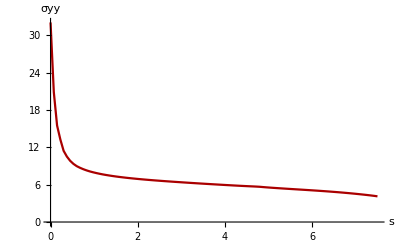

```mathematica
nx=100;
S=L-a;
σy=Table[
{S(i-1)/nx,
SMTPostData["σyy",Point[{S(i-1)/nx+a,H/2}]]},
{i,1,nx+1}];
ListLinePlot[σy,AxesLabel->{"s","σyy"},PlotStyle->Darker[Red],LabelStyle->Directive[FontSize->14,FontFamily->"Times",Black],PlotRange->{{0,S},{0,All}}]
```